```mathematica
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
```

```mathematica
(* Nuclear E2=2.22 E3=8.48 ℏc=198*)
LEC={
{1.00,1,-44.4515,27.245},
{2.00,1,-142.376,173.925},
{3.00,1,-295.93,566.65},
{4.00,1,-505.15,1426.75},
{6.00,1,-1090.548,6552.5},
{8.00,1,-1898.553,25697},
{10.0,1,-2929.165,92495}};
```

```mathematica
RiccatiBesselJ[z_,l_]:=z SphericalBesselJ[l,z];
RiccatiBesselN[z_,l_]:=z SphericalBesselY[l,z];
```

```mathematica
VlocTF[r_,lam_,Cc_,Dd_,Aa_]:=Block[{eta2,eta3,w2,w3},
eta2=2 Cc (3 Aa/(3 Aa+lam))^(3/2);
w2=3 Aa lam/(3 Aa+lam);
eta3=8 Dd (3 Aa^2/(12 Aa^2+16 Aa lam+lam^2))^(3/2);
w3=(12 Aa lam (Aa+lam)/(12 Aa^2+16 Aa lam+lam^2));
eta2 Exp[-w2 r^2]+eta3  Exp[-w3 r^2]
];

WnolocTF[r_,rp_,Ee_,lam_,Cc_,Dd_,Aa_,Ll_,TwoMyOverHBsq_]:=Block[{zeta1,zeta2,zeta3,a1,b1,c1,a2,b2,c2,a3,b3,c3},
zeta1=(27/8)(3/2 Aa)^(3/2) (1./TwoMyOverHBsq);
a1=(Aa 15/16);
b1=(Aa 18/16);
c1=a1;

zeta2=-2 27 (Aa 3/2)^(3./2) Cc (Aa/(4 Aa+lam))^(3/2);
zeta3=-27 (Aa 3/2)^(3./2) Dd (Aa/(4 Aa+5 lam))^(3/2);

a2=3 Aa (5 Aa+8 lam)/(4 (4 Aa+lam));
b2=9 Aa (Aa+lam)/(2 (4 Aa+lam));
c2=3 Aa (5 Aa+2 lam)/(4 (4 Aa+lam));

a3=3 (20 Aa^2+52 Aa lam+27 lam^2)/(4 (16 Aa+20 lam));
b3=9 (4 Aa^2+8 Aa lam+3 lam^2)/(2 (16 Aa+20 lam));
c3=3 (20 Aa^2+28 Aa lam+3 lam^2)/(4 (16 Aa+20 lam));

-(4 Pi r rp) (
zeta1 Exp[-a1 (r^2+rp^2)] ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)+(Ll+1) Ll/r^2-TwoMyOverHBsq Ee) I^Ll  SphericalBesselJ[Ll,I b1 r rp]
-4 a1 b1 r rp Sum[(1-Ll^2+l^2) I^(l+1)/Sqrt[3] (2/Sqrt[5])^((Ll+l)/2) SphericalBesselJ[1+l,I b1 r rp],{l,-Ll,Ll}])
+I^Ll zeta2 SphericalBesselJ[Ll,I b2 r rp] Exp[-a2 r^2-c2 rp^2]
+I^Ll zeta3 SphericalBesselJ[Ll,I b3 r rp] Exp[-a3 r^2-c3 rp^2]
)
];
```

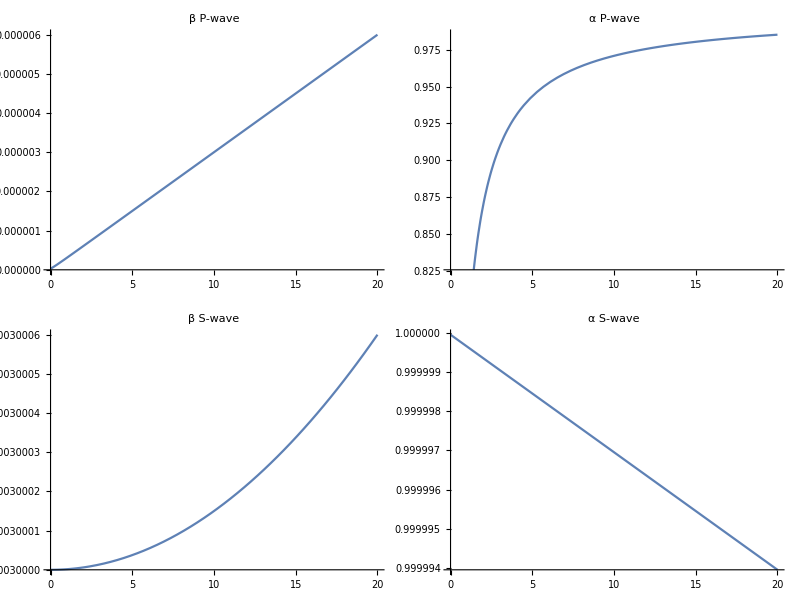

```mathematica
alpha[ra_,ka_,la_,ha_]:=RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]


beta[rb_,kb_,lb_,hb_]:= RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])

nGrid=100;
rmm=20;
Grid[{{Plot[{beta[rv,k0FM,1,rr/nGrid]},{rv,0,rmm},PlotLabel->"β P-wave"],Plot[alpha[rv,k0FM,1,rr/nGrid],{rv,0,rmm},PlotLabel->"α P-wave"]},{
Plot[beta[rv,k0FM,0,rr/nGrid],{rv,0,rmm},PlotLabel->"β S-wave"],Plot[alpha[rv,k0FM,0,rr/nGrid],{rv,0,rmm},PlotLabel->"α S-wave"]}}]
```

The function <SolveSecular> expects the variable <<momentum>> in  [fm^-1]
As  W_(non-local) takes the Energy (e_) in [MeV],

```mathematica
SolveSecular[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a0_?NumberQ,cfg0_?ArrayQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV},

hDif=N[Rdis/Npoints];
energyMeV=(momentum^2)/TwoMyOverHBsq;

Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];

Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a0]-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];

Wmat=Table[-hDif^3 TwoMyOverHBsq WnolocTF[i hDif,j hDif,energyMeV,lam,c0,d0,a0,Lin,TwoMyOverHBsq],{i,1,Npoints},{j,1,Npoints}]; 

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

Amat=Dmat+Kmat+Wmat;

bcol⟦-1⟧= -beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

tanDelta=(RiccatiBesselJ[momentum Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);

tanDelta
]
```

```mathematica
cfg={3,1};
Switch[cfg[[1]],
2,afit=6.;rr=30,
3,afit=2.;rr=30; 
];
hbar=197.327053;
Mm=938.92;
m1=cfg[[1]] Mm;m2=cfg[[2]] Mm;
μ=m1 m2/(m1+m2);mh2=(2 μ)/(hbar)^2;
Print["E_0 = ",(k0FM hbar)^2/(2 μ)," MeV"]
λRange=Range[Length[LEC]-2,Length[LEC]];
```

E_0 = 0.0000276473 MeV

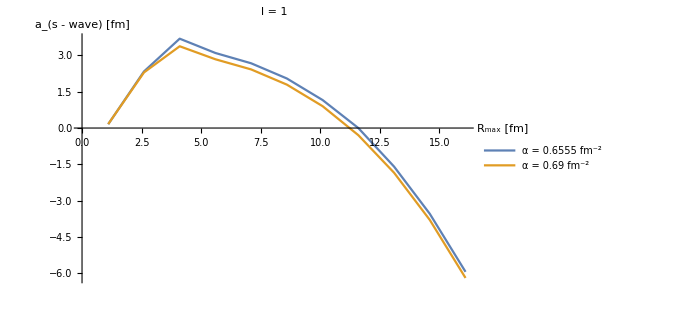

```mathematica
Lrel=1;
aOfa={};
aini=0.69;
αRange=Subdivide[0.95 aini,aini,1];
rRange=Subdivide[1.1,16.1,10];
k0FM=0.001;
nGrid=100;
Do[
aS={};
SetSharedVariable[aS];
nn=Length[LEC];
ParallelDo[
λ=0.25 LEC⟦nn⟧[[1]]^2;C0=LEC⟦nn⟧[[3]];D0=LEC⟦nn⟧[[4]];
TanDelSwave=Chop[SolveSecular[rr,nGrid,k0FM,Lrel,λ,C0,D0,α0,cfg,mh2]];
AppendTo[aS,{rr,-TanDelSwave/k0FM^(2 Lrel+1)}];
,{rr,rRange}];
a0=Reverse[Sort[aS,#1[[1]]>#2[[1]]&]];
AppendTo[aOfa,a0];
,{α0,αRange}];
leg="α = "<>ToString[#]<>" fm^-2"&/@αRange;
ListPlot[aOfa,AxesLabel->{"R_max [fm]","a_(s - wave) [fm]"},ImageSize->500,PlotLegends->leg,PlotRange->Automatic,Joined->True,PlotLabel->Style["l = "<>ToString[Lrel],Orange,16]]
```